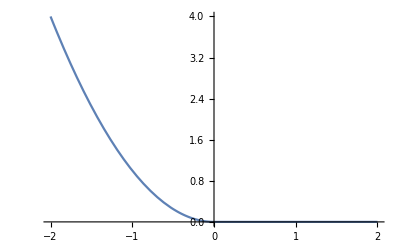

```mathematica
Plot[u[x],{x,-2,2}]
```

```mathematica
u[x_]:=Piecewise[{{x^2, x<0}, {0, True}}]
```

```mathematica
Limit[Exp[-π/t^2]/t,{t-> 0}]
```

{0}

```mathematica
D[Exp[x/t^2],t]
```

-(2 ⅇ^(x/t^2) x)/t^3

```mathematica
f[t_]:=Integrate[(2π t)^(-1/2) Exp[-x^2/(2t)],{x,a t,∞}];f[t]
```

```mathematica
1/2 Erfc[(a √t)/(√2)]/.t->0
```

1/2

```mathematica
$Assumptions=t>0;
```

```mathematica
Plot[f[t],{t,0.001,1}]
```

-Graphics-

```mathematica
1/2 √π Erfc[0]
```

(√π)/2

```mathematica
p[d_]:=a d-b d^2
```

```mathematica
u[x_]:=Piecewise[{{(a x)^2/2 -a x, x<0}, {Exp[-a x]-1, True}}]
```

```mathematica
u''[0]
```

a^2

```mathematica
g[x_]:=D[u[y],y]/.y-> x
```

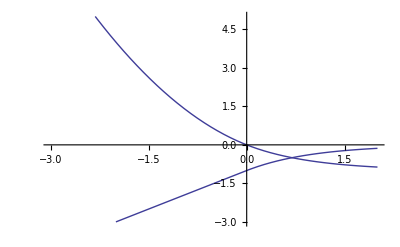

```mathematica
Plot[{u[x],g[x]}/.{a->1},{x,-3,2},PlotRange->{-3,5}]
```

```mathematica
Animate[Plot[{u[x]/.a->b},{x,-3,2},PlotRange->{-1,5}],{b,.1,2}]
```

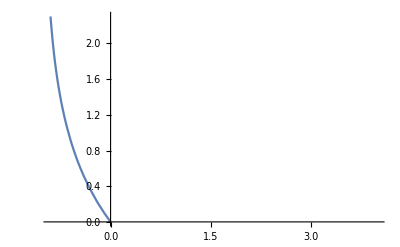

```mathematica
Plot[g[x],{x,-.9,4}]
```